# Finite Wing Project For the NACA 23012 Airfoil

Mohammad Khaled Gamal Ali

Sec:2,BN:14

## Clearing any old data

```mathematica
ClearAll["Global`*"]
```

## Initialization of the variables

```mathematica
SEC=2.; Bn=14.; V∞=51.;
ρ= 1.225;
Cr =SEC/2.+Bn/80.;
Ct =SEC/3.+Bn/120.;
b = 4.*(Cr + Ct);
α= (10. -Bn/10.)*π/180;
α0 = -1.1 *π/180;
a0 =6.178;
S = (b*(Cr + Ct))/2;
AR =b^2/S;

Δy = b/6;

y = {0.5 *Δy, 1.5 *Δy, 2.5 *Δy};

θ=ArcCos[-2 *y/b   ];


c = Cr - y*(Cr - Ct)/(b/2);
μ=(c*a0)/(4 b);
```

## Solving the monoplane equation

```mathematica
AMOGUS=μ (α-α0) Sin[θ];
SUS=Table[((2 i-1)*μ⟦j⟧+Sin[θ⟦j⟧])*Sin[(2 i-1)*θ⟦j⟧],{j,3},{i,3}];
SUSSY=LinearSolve[SUS,AMOGUS];
```

## Calculations of the lift coefficient and the drag coefficient

```mathematica
CL=π*SUSSY⟦1⟧*AR;
δ=Sum[n*(SUSSY⟦n⟧/SUSSY⟦1⟧)^2,{n,2,3}];
CDi=CL^2 (1+δ)/(π*AR);
Lift=0.5*ρ*(V∞)^2*S*CL;
Drag=0.5*ρ*(V∞)^2*S*CDi;
```

## Displaying the output

```mathematica
Row[{HoldForm@CL," = ",ReleaseHold@CL}]
Row[{HoldForm@CDi," = ",ReleaseHold@CDi}]
Row[{HoldForm@Lift," = ",ReleaseHold@Lift," N"}]
Row[{HoldForm@Drag," = ",ReleaseHold@Drag," N"}]
```

CL = 0.816719

CDi = 0.0268875

Lift = 9979.81 N

Drag = 328.548 N

## Drawing the wing planform

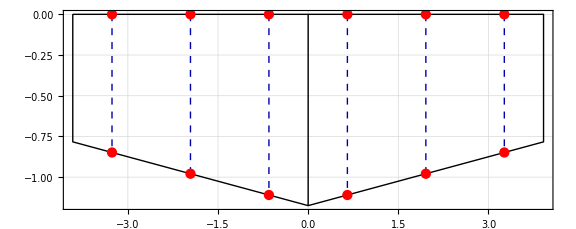

```mathematica
RStations=Line[Table[{{y⟦i⟧,0},{y⟦i⟧,-c⟦i⟧}},{i,3}]];
LStations=Line[Table[{{-y⟦i⟧,0},{-y⟦i⟧,-c⟦i⟧}},{i,3}]];
P1=Table[{y⟦i⟧,0},{i,3}];
P2=Table[{y⟦i⟧,-c⟦i⟧},{i,3}];
P3=Table[{-y⟦i⟧,0},{i,3}];
P4=Table[{-y⟦i⟧,-c⟦i⟧},{i,3}];
Append[Append[Append[P1,P2],P3],P4];
points=ArrayReshape[Append[Append[Append[P1,P2],P3],P4],{1,12,2}];
WingEq=Line[{{-b/2,0},{-b/2,-Ct},{0,-Cr},{b/2,-Ct},{b/2,0},{-b/2,0}}];
CenterLine=Line[{{0,0},{0,-Cr}}];
Show[Graphics[{{Thick,WingEq},{Thick,CenterLine},{Thick,Dashed,Darker[Blue],RStations},{Thick,Dashed,Darker[Blue],LStations}},ImageSize->Large,GridLines->Automatic,Frame->True],Graphics[ListPlot[points,PlotStyle->{Red}]]]
```